Министерство образования и науки Российской Федерации
Федеральное государственное бюджетное образовательное учреждение
высшего профессионального образования
«Национальный исследовательский Томский политехнический университет»

Институт: ИЯТШ
Отделение прикладной математики и информатики

ОТЧЕТ ПО ЛАБОРАТОРНОЙ РАБОТЕ №3
 Одномерные колебания. Метод Даламбера
Вариант №18

Выполнил: студент группы 0В01
Саматов Денис
Проверил: Богданов О.В.

Задание 1
	Дана конечная струна длинны L=1, закрепленная на концах. Начальное смещение ноль и f(x, t) = 0. Начальная скорость представлена на рисунке. Построить профиль струны.

-Graphics-

```mathematica
L=1;a=1;T=Range[0,1.98,0.02];
```

```mathematica
stc[x_,w_]=Abs[x-w Floor[x/w+1/2]];
```

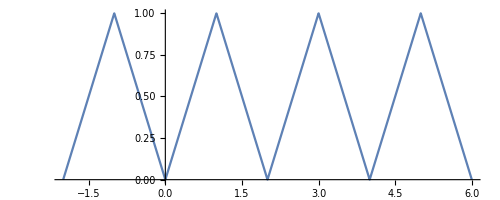

```mathematica
Plot[stc[x,2],{x,-2,6},AspectRatio->Automatic]
```

```mathematica
ψ1[x_]=Piecewise[{{1,0.2<=x<=0.3},{1,0.7<=x<=0.8}},0];
```

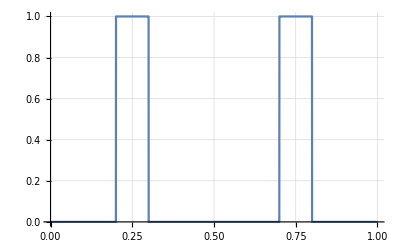

```mathematica
Plot[ψ1[x],{x,0,1},Exclusions->None,GridLines->Automatic]
```

```mathematica
v1[x_,t_]=1/(2a)Simplify[Integrate[ψ1[τ],{τ,α,β},Assumptions->α>0 && β>0]];
```

```mathematica
u1[x_,t_]=v1[x,t]/.{α->stc[x-a*t, 2*L], β->stc[x+a*t,2*L]};
```

```mathematica
Animate[Plot[u1[x,t],{x,0,1}, PlotRange->{-0.12,0.12}, PlotLabel->t, Exclusions->None, GridLines->Automatic],{t,T},AnimationRunning->False]
```

Задание 2
	Дана конечная струна длинны L=1, закрепленная на концах. В начальный момент скорость равна нулю и f(x, t) = 0, а начальное отклонение представлено на рисунке. Построить профиль струны.

-Graphics-

```mathematica
ψ2[x_]=0;
```

```mathematica
ϕ2[x_]=Piecewise[{{x-0.6,0.4<=x<=0.8}},0];
```

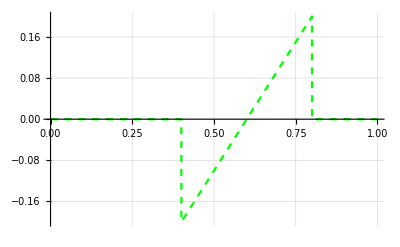

```mathematica
Plot[ϕ2[t],{t,0,1},Exclusions->None, PlotStyle->{Dashed, Green},GridLines->Automatic]
```

```mathematica
v2[x_,t_]=(ϕ2[x+a*t]+ϕ2[x-a*t])/2+1/(2a)Simplify[Integrate[ψ2[τ],{τ,α,β},Assumptions->α>0 && β>0]];
```

```mathematica
u2[x_,t_]=v2[x,t]/.{α->stc[x-a*t, 2*L], β->stc[x+a* t,2*L]};
```

```mathematica
Animate[Plot[u2[x,t],{x,0,1}, PlotRange->{-0.25,0.25}, PlotLabel->t, Exclusions->None, GridLines->Automatic],{t,T},AnimationRunning->False]
```

Задание 3
	Дана конечная струна длинны L=1, закрепленная на концах. В начальный момент f(x, t) = 0, а начальное отклонение и скорость представлены на рисунке. Построить профиль струны.

-Graphics-

```mathematica
ψ3[x_]=Piecewise[{{1,0.5<=x<=0.6}},0];
```

```mathematica
ϕ3[x_]=Piecewise[{{5*x-3,0.6<=x<=0.8}},0];
```

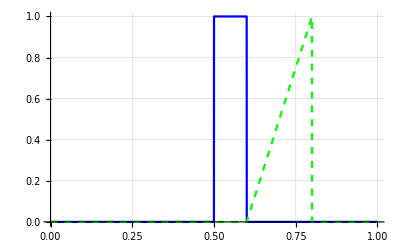

```mathematica
Plot[{ψ3[t],ϕ3[t]},{t,0,1},Exclusions->None,GridLines->Automatic,PlotStyle->{Blue,{Dashed, Green}}]
```

```mathematica
v3[x_,t_]=(ϕ3[x+a*t]+ϕ3[x-a*t])/2+1/(2a)Simplify[Integrate[ψ3[τ],{τ,α,β},Assumptions->α>0 && β>0]];
```

```mathematica
u3[x_,t_]=v3[x,t]/.{α->stc[x-a*t, 2 *L], β->stc[x+a*t,2*L]};
```

```mathematica
Animate[Plot[u3[x,t],{x,0,1}, PlotRange->{-0.2,1}, PlotLabel->t, Exclusions->None, GridLines->Automatic],{t,T},AnimationRunning->False]
```

Вывод:
	В ходе выполнения лабораторной работы изучено общее решение Даламбера задачи:-Graphics- для неограниченной прямой.
	Кроме этого были построены профили струны в зависимости от заданных начальных параметров: начального отклонения струны и начальной скорости струны.
	1) В первом задании профиль струны был построен при условии, что начальное смещение ноль и f(x, t) = 0.  Кроме этого начальная скорость была представлена на рисунке.
	2) Во  втором задании профиль струны был построен при условии, что в начальный момент скорость равна нулю и f(x, t) = 0, а начальное отклонение  было представлено на рисунке.
	3) В третьем задании профиль струны был построен при условии, что в начальный момент f(x, t) = 0, а начальное отклонение и скорость были представлены на рисунке. 
	Также в результате написания программного кода были изучены новые функции: Animate[] и Piecewise[].